```mathematica
<<Figures`Basic`;
<<Figures`Color`;
<<Figures`Ticks`;
<<Figures`MultiPanel`;
<<Figures`Markers`;
<<Figures`Legends`;
```

```mathematica
En[0]=Import[NotebookDirectory[]<>"results/En_0.dat"];
En[1]=Import[NotebookDirectory[]<>"results/En_1.dat"];
En[2]=Import[NotebookDirectory[]<>"results/En_2.dat"];
```

```mathematica
En[0]⟦1,2⟧
En[1]⟦1,2⟧
En[2]⟦1,2⟧
```

6.79506

8.58193

10.1978

```mathematica
ϕ[0]=Interpolation[Import[NotebookDirectory[]<>"results/WFvac_0_0.dat"]];
ϕ[1]=Interpolation[Import[NotebookDirectory[]<>"results/WFvac_1_0.dat"]];
ϕ[2]=Interpolation[Import[NotebookDirectory[]<>"results/WFvac_2_0.dat"]];
xmax=2.5;
```

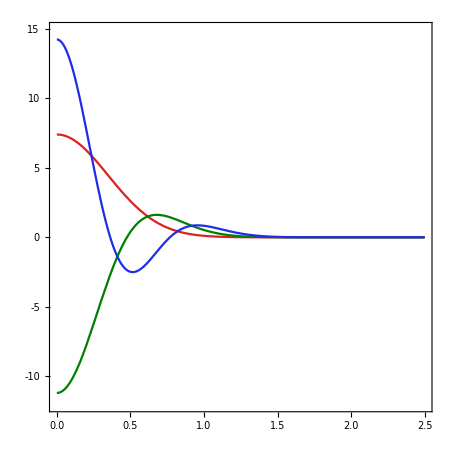

```mathematica
Plot[{ϕ[0][x],ϕ[1][x],ϕ[2][x]},{x,0,xmax},PlotRange->{-12,14.9},PlotStyle->{Red,Green,Blue}]//Quiet
```

```mathematica
m=5;
Do[
I1=NIntegrate[(m r^2(ϕ[ist][r])^2 r^2)/(En[ist]⟦1,2⟧+m-m/2 r^2),{r,0,xmax}]//Quiet;
I2=2NIntegrate[(En[ist]⟦1,2⟧-m/2 r^2)(ϕ[ist][r])^2 r^2,{r,0,xmax}]//Quiet;
I3=-NIntegrate[(m ϕ[ist][r](r D[ϕ[ist][r],r]-ϕ[ist][r]))/((En[ist]⟦1,2⟧+m-m/2 r^2)^2)r^2,{r,0,xmax}]//Quiet;
fac[ist]=1/2(-2+4/3 I1)/(I2+I3);
,{ist,0,2}]
```

```mathematica
MultiPanel[{
Show[{ListPlot[Transpose[{En[2]⟦;;,1⟧,En[2]⟦;;,2⟧}],Joined->True,PlotStyle->Directive[Blue,AbsoluteThickness[1.2]]],
Plot[En[2]⟦1,2⟧-fac[2]x,{x,0,1},PlotStyle->Directive[Blue,AbsoluteThickness[2],AbsoluteDashing[{5,7}]]]
},PlotRange->{{0,1},{10.195,10.255}},Epilog->{Inset[Style["n = 2",FontFamily->"Times New Roman",25],Scaled[{0.2,0.8}]],
Inset[Style["exact",FontFamily->"Times New Roman",25],{0.6,6.82},{Left,Center}],
Inset[Style["perturbative",FontFamily->"Times New Roman",25],{0.6,6.805},{Left,Center}]},AspectRatio->0.5]
,
Show[{ListPlot[Transpose[{En[1]⟦;;,1⟧,En[1]⟦;;,2⟧}],Joined->True,PlotStyle->Directive[Green,AbsoluteThickness[1.2]]],
Plot[En[1]⟦1,2⟧-fac[1]x,{x,0,1},PlotStyle->Directive[Green,AbsoluteThickness[2],AbsoluteDashing[{5,7}]]]},PlotRange->{{0,1},{8.581,8.649}},Epilog->{Inset[Style["n = 1",FontFamily->"Times New Roman",25],Scaled[{0.2,0.8}]],
Inset[Style["exact",FontFamily->"Times New Roman",25],{0.6,6.82},{Left,Center}],
Inset[Style["perturbative",FontFamily->"Times New Roman",25],{0.6,6.805},{Left,Center}]},AspectRatio->0.5,FrameLabel->{"","E_n [ω]"}]
,
Show[{
ListPlot[Transpose[{En[0]⟦;;,1⟧,En[0]⟦;;,2⟧}],Joined->True,PlotStyle->Directive[Red,AbsoluteThickness[1.2]]],
Plot[En[0]⟦1,2⟧-fac[0]x,{x,0,1},PlotStyle->Directive[Red,AbsoluteThickness[2],AbsoluteDashing[{5,7}]]],
ListPlot[{{{0.45,6.82},{0.57,6.82}},{{0.45,6.805},{0.57,6.805}}},Joined->True,PlotStyle->{Directive[Black,AbsoluteThickness[1.2]],Directive[Black,AbsoluteThickness[2],AbsoluteDashing[{5,7}]]}]},
PlotRange->{{0,1},{6.79,6.8799}},Epilog->{Inset[Style["n = 0",FontFamily->"Times New Roman",25],Scaled[{0.2,0.8}]],
Inset[Style["complete",FontFamily->"Times New Roman",25],{0.6,6.82},{Left,Center}],
Inset[Style["perturbative",FontFamily->"Times New Roman",25],{0.6,6.805},{Left,Center}]},AspectRatio->0.5,FrameLabel->{"B [ω^2]",""}]},AspectRatio->0.4]
```

-Graphics-

```mathematica
Do[ϕB[n,j]=Interpolation[Import[NotebookDirectory[]<>"results/WFB_"<>ToString[n]<>"_"<>ToString[j]<>".dat"]];,{n,0,2},{j,0,9}]
```

```mathematica
Quiet[
MultiPanel[{
Show[Table[Plot[ϕB[2,j][x],{x,0,xmax},PlotRange->{{0,xmax},{-3,14.9}},PlotStyle->ColorData["Rainbow",1-j/9]],{j,0,9}],FrameLabel->{"",""},Epilog->{Inset[Style["n = 2",FontFamily->"Times New Roman",25],Scaled[{0.8,0.8}]]},AspectRatio->0.4],
Show[Table[Plot[-ϕB[1,j][x],{x,0,xmax},PlotRange->{{0,xmax},{-3,12.9}},PlotStyle->ColorData["Rainbow",1-j/9]],{j,0,9}],FrameLabel->{"","ϕ_n [ω^(3/2)]"},Epilog->{Inset[Style["n = 1",FontFamily->"Times New Roman",25],Scaled[{0.8,0.8}]]},AspectRatio->0.4],
Show[Table[Plot[ϕB[0,j][x],{x,0,xmax},PlotRange->{{0,xmax},{-1,8.9}},PlotStyle->ColorData["Rainbow",1-j/9]],{j,0,9}],FrameLabel->{"r [ω^-1]",""},Epilog->{Inset[Style["n = 0",FontFamily->"Times New Roman",25],Scaled[{0.8,0.8}]],
Inset[Style["qB = ω^2",FontFamily->"Times New Roman",25],Scaled[{0.8,0.6}]]},AspectRatio->0.4]
},AspectRatio->0.4]
]
```

-Graphics-